# Density Plot

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"clean"]

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=170/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

max dv=12.5952

## Test Design

#### Pythagoras

```mathematica
pyth[{x_,y_}]:=Sqrt[(x^2+y^2)]
```

#### RMSE

```mathematica
rmse[x_,y_]:=N@Sqrt[Mean[Power[x-y,2]]]
```

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

#### count colors

```mathematica
(*Counts the amount of colors in solution*)
countColors[v_]:=Block[{count},
count=0;
ImageScan[If[Mean[#]≠0,count++]&,v];
count
]
```

#### N tests

```mathematica
(*Error is updated depending in the highest res level *)
test1[ia_,ib_,lvlmax_,e_,mode_]:=Block[{},(

Table[
stereoDepth[ia,ib,lvlmax,{1,i},e,mode]
,{i,lvlmax}]

)]
```

#### results

```mathematica
res1Display[res1_,id_]:=Block[{maxid,flipMask, signMask, magMask, okMask, convergedMask,imageConverged, imageOk, imageFlip, imageSign, imageMag},(
maxid=MinMax[Flatten[ImageData[id]]][[2]];
npixels=103.*45.;

(*"converged", "ok","oksign","flip","sign","mag"*)
flipMask={"converged"->Transparent,"ok"->Transparent,"oksign"->Transparent,"flip"->Orange,"sign"->Transparent,"mag"->Transparent};
signMask={"converged"->Transparent,"ok"->Transparent,"oksign"->Transparent,"flip"->Transparent,"sign"->Red,"mag"->Transparent};
magMask={"converged"->Transparent,"ok"->Transparent,"oksign"->Transparent,"flip"->Transparent,"sign"->Transparent,"mag"->Purple};
okMask={"converged"->Transparent,"ok"->Pink,"oksign"->Blue,"flip"->Transparent,"sign"->Transparent,"mag"->Transparent};
convergedMask={"converged"->Green,"ok"->Transparent,"oksign"->Transparent,"flip"->Transparent,"sign"->Transparent,"mag"->Transparent};

Table[
imageConverged=Image[res[[All,All,2]]/.convergedMask];
imageOk=Image[res[[All,All,2]]/.okMask];
imageFlip=Image[res[[All,All,2]]/.flipMask];
imageSign=Image[res[[All,All,2]]/.signMask];
imageMag=Image[res[[All,All,2]]/.magMask];

lst1=Flatten[-res[[All,All,1]]];
lst2=Flatten[ImageData[id]];
p=Flatten[Position[Flatten[res[[All,All,2]]],#]&/@{"sign","mag","flip","ok","oksign"},1];
lst11=Delete[lst1,p];
lst22=Delete[lst2,p];

{Image[-res[[All,All,1]]]/(maxid),
id/(maxid),
Grid[{{imageConverged},{countColors[imageConverged]}}],
Grid[{{imageOk},{countColors[imageOk]}}],
Grid[{{imageFlip},{countColors[imageFlip]}}],
Grid[{{imageSign},{countColors[imageSign]}}],
Grid[{{imageMag},{countColors[imageMag]}}],
rmse[lst11,lst22],
rmse[lst1,lst2],
npixels/countColors[imageConverged]
}
,{res, res1}]
)]
```

#### Display of results

```mathematica
res2ColorCode[result_,id_]:=Block[{},(
minmaxid=MinMax[Flatten[ImageData[id]]];
(*seeStatus={"converged"->Transparent,"ok"->Transparent,"flip"->Red,"sign"->Purple,"mag"->Yellow};*)
flipMask={"converged"->Transparent,"ok"->Transparent,"flip"->Orange,"sign"->Transparent,"oksign"->Transparent,"mag"->Transparent};
signMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Red,"oksign"->Transparent,"mag"->Transparent};
magMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"oksign"->Transparent,"mag"->Purple};
okMask={"converged"->Transparent,"ok"->Pink,"flip"->Transparent,"sign"->Transparent,"oksign"->Blue,"mag"->Transparent};
convergedMask={"converged"->Green,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"oksign"->Transparent,"mag"->Transparent};

imageConverged=Image[result[[All,All,2]]/.convergedMask];
imageOk=Image[result[[All,All,2]]/.okMask];
imageFlip=Image[result[[All,All,2]]/.flipMask];
imageSign=Image[result[[All,All,2]]/.signMask];
imageMag=Image[result[[All,All,2]]/.magMask];

{Image[-result[[All,All,1]]]/(minmaxid[[2]]),
id/(minmaxid[[2]]),
Grid[{{imageConverged},{countColors[imageConverged]}}],
Grid[{{imageOk},{countColors[imageOk]}}],
Grid[{{imageFlip},{countColors[imageFlip]}}],
Grid[{{imageSign},{countColors[imageSign]}}],
Grid[{{imageMag},{countColors[imageMag]}}]}

)]
```

## Calculating results

```mathematica
e=0.01;
lvls=4;
```

#### OverConstrained {1, n} test

```mathematica
mode="OverConstrained";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
404,-Graphics-
89,-Graphics-
0,-Graphics-
2947,-Graphics-
1195,5.3849,6.54468,11.4728},{-Graphics-,-Graphics-,-Graphics-
452,-Graphics-
5,-Graphics-
0,-Graphics-
3139,-Graphics-
1039,4.43152,6.45132,10.2544},{-Graphics-,-Graphics-,-Graphics-
722,-Graphics-
6,-Graphics-
0,-Graphics-
3143,-Graphics-
764,2.86171,6.21138,6.41967},{-Graphics-,-Graphics-,-Graphics-
1109,-Graphics-
10,-Graphics-
0,-Graphics-
2689,-Graphics-
827,2.22194,5.9427,4.17944}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

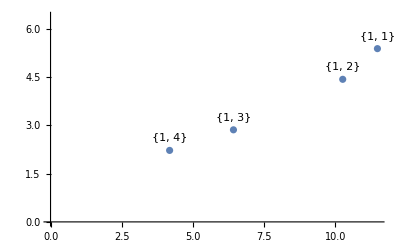

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0,maxX+0.001},{0,maxY+1}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### SemiConstrained {1, n} test

```mathematica
mode="SemiConstrained";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
404,-Graphics-
89,-Graphics-
0,-Graphics-
2947,-Graphics-
1195,5.3849,6.51366,11.4728},{-Graphics-,-Graphics-,-Graphics-
695,-Graphics-
58,-Graphics-
0,-Graphics-
2863,-Graphics-
1019,4.94613,6.64736,6.66906},{-Graphics-,-Graphics-,-Graphics-
1188,-Graphics-
68,-Graphics-
0,-Graphics-
2442,-Graphics-
937,4.25226,6.34153,3.90152},{-Graphics-,-Graphics-,-Graphics-
1737,-Graphics-
85,-Graphics-
0,-Graphics-
1932,-Graphics-
881,3.89924,5.80527,2.66839}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

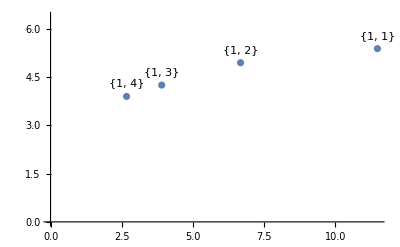

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0,maxX+0.001},{0,maxY+1}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Constrained {1, n} test

```mathematica
mode="Constrained";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
404,-Graphics-
89,-Graphics-
0,-Graphics-
2947,-Graphics-
1195,5.3849,6.51366,11.4728},{-Graphics-,-Graphics-,-Graphics-
695,-Graphics-
58,-Graphics-
0,-Graphics-
2863,-Graphics-
1019,4.94613,6.4338,6.66906},{-Graphics-,-Graphics-,-Graphics-
980,-Graphics-
11,-Graphics-
0,-Graphics-
2782,-Graphics-
862,3.7896,6.08478,4.72959},{-Graphics-,-Graphics-,-Graphics-
1440,-Graphics-
33,-Graphics-
0,-Graphics-
2473,-Graphics-
689,3.03893,5.66392,3.21875}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

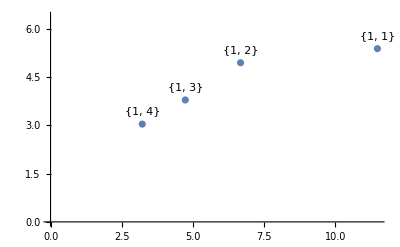

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0,maxX+0.001},{0,maxY+1}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Constrained Initial Sign {1, n} test

```mathematica
mode="ConstrainedInitialSign";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
625,-Graphics-
125,-Graphics-
0,-Graphics-
1255,-Graphics-
2630,6.01891,7.09774,7.416},{-Graphics-,-Graphics-,-Graphics-
1136,-Graphics-
93,-Graphics-
0,-Graphics-
1304,-Graphics-
2102,5.57001,7.89775,4.08011},{-Graphics-,-Graphics-,-Graphics-
1600,-Graphics-
35,-Graphics-
0,-Graphics-
1270,-Graphics-
1730,5.05027,6.11072,2.89688},{-Graphics-,-Graphics-,-Graphics-
1817,-Graphics-
45,-Graphics-
0,-Graphics-
1326,-Graphics-
1447,4.4081,5.52702,2.55091}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

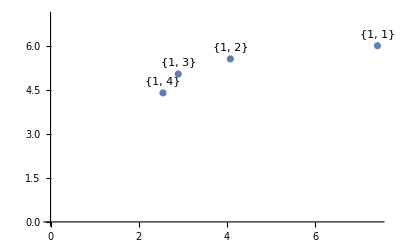

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0,maxX+0.001},{0,maxY+1}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### Constrained New Method {1, n} test

```mathematica
mode="ConstrainedNewMethod";
```

```mathematica
Subscript[res1, mode]=test1[ia,ib, lvls,e,mode];
```

```mathematica
Subscript[res1Dis, mode]=res1Display[Subscript[res1, mode],id]
```

{{-Graphics-,-Graphics-,-Graphics-
404,-Graphics-
89,-Graphics-
0,-Graphics-
2947,-Graphics-
1195,5.3849,6.51366,11.4728},{-Graphics-,-Graphics-,-Graphics-
234,-Graphics-
39,-Graphics-
0,-Graphics-
3110,-Graphics-
1252,5.5586,6.42026,19.8077},{-Graphics-,-Graphics-,-Graphics-
61,-Graphics-
0,-Graphics-
0,-Graphics-
3281,-Graphics-
1293,5.59566,6.29271,75.9836},{-Graphics-,-Graphics-,-Graphics-
12,-Graphics-
1,-Graphics-
0,-Graphics-
3304,-Graphics-
1318,4.45247,6.44073,386.25}}

```mathematica
Subscript[errorRMSE, mode]=Subscript[res1Dis, mode][[All,-3]];
Subscript[density, mode]=Subscript[res1Dis, mode][[All,-1]];
```

```mathematica
Subscript[densityRes, mode]=Flatten[{Subscript[density, mode],Subscript[errorRMSE, mode]},{{2},{1}}];
```

```mathematica
(* Plot values *)
offset={0,0.4};
{maxX,maxY}={Max[Subscript[densityRes, mode][[All,1]]],Max[Subscript[densityRes, mode][[All,2]]]};
```

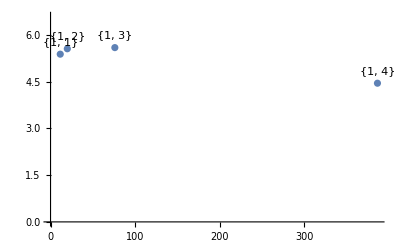

```mathematica
Show[
ListPlot[Subscript[densityRes, mode],PlotRange->{{0,maxX+0.001},{0,maxY+1}}],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
]
```

#### All {1, n} test

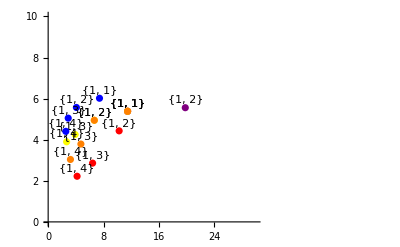

```mathematica
(* Closest Value to {0,0} wins *)
rangexyPlot={{0,30},{0,10}};
Show[{
mode="OverConstrained";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Red],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],
mode="SemiConstrained";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Yellow],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],
mode="Constrained";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Orange],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],
mode="ConstrainedInitialSign";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Blue],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}],
mode="ConstrainedNewMethod";
ListPlot[Subscript[densityRes, mode],PlotRange->rangexyPlot,PlotStyle->Purple],
Graphics@Text[ToString@#[[1]],#[[2]]+offset]&/@Table[{{1,n},Subscript[densityRes, mode][[n]]},{n,1,lvls}]
}]
```

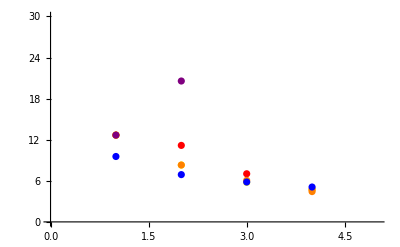

```mathematica
(* Smallest value Wins *)
rangexyPlot={{0,lvls+1},{0,30}};
Show[{
mode="OverConstrained";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Red,PlotRange->rangexyPlot],
mode="SemiConstrained";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Yellow],
mode="Constrained";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Orange],
mode="ConstrainedInitialSign";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Blue],
mode="ConstrainedNewMethod";
ListPlot[pyth[#]&/@Subscript[densityRes, mode],PlotStyle->Purple]
},
ImageSize->Scaled[0.5]]
```